```mathematica
ainns[B_]:=abg(1+Δ/(B-Bo))(1+α(B-Bo))
```

```mathematica
Cinns={abg->-1405 ao,Bo->834 G, Δ->300 G,α->4*^-4 /G}
```

{abg→-1405 ao,Bo→834 G,Δ→300 G,α→1/(2500 G)}

```mathematica
arice[B_]:=abg(1+Δ/(B-Bo))
```

```mathematica
Crice={abg->-1580 ao,Bo->834 G, Δ->270 G}
```

{abg→-1580 ao,Bo→834 G,Δ→270 G}

```mathematica
100+163.7-1.414*86*6.8
```

-563.207

```mathematica
Table[ainns[6.8 Current  G]/.Cinns,{Current,{83,86,90,93,96,99,85}}]
```

{141.342 ao,257.863 ao,449.813 ao,630.473 ao,854.393 ao,1138.04 ao,216.756 ao}

```mathematica
6.8*92
```

625.6

```mathematica
(668+747)/2.
```

707.5

```mathematica
Exp[-2*1/2.75^2]
```

0.767618

```mathematica
Table[arice[6.8 Current  G ]/.Crice,{Current,{83,86,90,93,96,99,85}}]
```

{2.34421 ao,131.878 ao,341.622 ao,536.071 ao,774.305 ao,1072.99 ao,86.4063 ao}

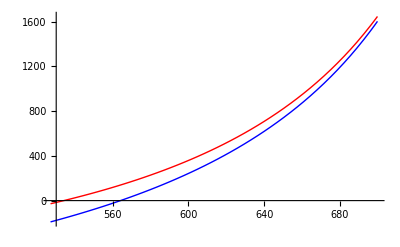

```mathematica
Plot[{ainns[B  G]/ao/.Cinns,arice[B  G ]/ao/.Crice/.Crice},{B,527,700},PlotStyle->{Red,Blue}]
```

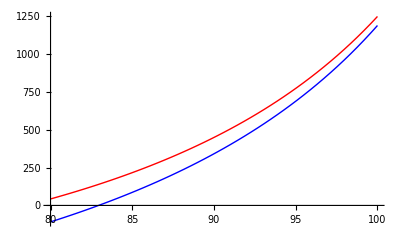

```mathematica
Plot[{ainns[6.8 Current  G]/ao/.Cinns,arice[6.8 Current  G ]/ao/.Crice/.Crice},{Current,80,100},PlotStyle->{Red,Blue}]
```

```mathematica
Clear[a_inns]
```

Clear::ssym: a_inns is not a symbol or a string.

```mathematica
77.5*6.8
```

527.

```mathematica
95*6.8
```

646.

```mathematica
arice[646. G ]/.Crice
ainns[646. G]/.Cinns
```

689.149 ao

774.077 ao

```mathematica
665/6.8
```

97.7941

```mathematica
80+163.7-665*1.414
```

-696.61

```mathematica
arice[89*6.8 G ]/.Crice
ainns[89*6.8 G]/.Cinns
```

284.51 ao

397.206 ao

```mathematica
89*6.8 G
```

605.2 G

```mathematica
d/wo((3Nsites)/(4 ℼ))^(1/3)
```

```mathematica
Solve [(d/wo((3Nsites)/(4 π))^(1/3)/.d->.532/.wo-> 42)==√(Log[3]/2.), Nsites]
```

{{Nsites→839118.}}

```mathematica
11.325969760936177 wo^6/.wo->42
```

6.21686×10^10

```mathematica
d/wo((3Nsites)/(4 π))^(1/3)/.wo->42/.d->.532/.Nsites->84^3
```

0.660053

```mathematica
2.ℼ
```

2. ℼ

```mathematica
d/1((3Nsites)/(4 π))^(1/3)/.wo->42/.d->.532/.Nsites->84^3
```

27.7222

```mathematica
√(3 42.^2)
```

72.7461

```mathematica
(2*84)^3
```

4741632

```mathematica
(2*42/.532)^3
```

3.93643×10^6

```mathematica
42/.532
```

78.9474

```mathematica
Solve[ⅇ^((-2r^2)/wo^2) ==1/3,r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→-wo √(Log[3]/2)},{r→wo √(Log[3]/2)},{r→-wo √(1/2 (-2 ⅈ π+Log[3]))},{r→wo √(1/2 (-2 ⅈ π+Log[3]))}}

```mathematica
√(Log[3]/2.)
```

0.741152